## Calcoli iniziali

```mathematica
Clear["Global`*"]
```

## # Dati iniziali

### # Tratti Rettangolari

```mathematica
dati={{"lunghezza", "spessore", "x centro tratto", "y centro tratto", "Pieno (1) o vuoto(-1)", "angolo sull'orizzontale"}, {2a, s, -a, 0, 1, π/2}, {a, 2s, -a/2, 0, 1, 0}, {√2 a, s, a/2, a/2, 1, π/4}, {√2 a, s, a/2, -a/2, 1, -π/4}, {a, 2s, a/2, a, 1, 0}, {a, 2s, a/2, -a, 1, 0}}[[2;;]];
```

### # Tratti Circolari

```mathematica
cerchio={{"spessore", "raggio", "Baricentro x", "Baricentro y"
"(2  a)/π", "Pieno (1) 
o vuoto(-1)", "angolo iniz", "angolo fin", X centro, Y centro}, {0, 0, 0, 0, 0, 0, 0, 0, 0}}[[2;;]];
```

## Calcoli (Area, CdF, Assi principali d’inerzia)

### Denominazione

#### Tratti Rettangolari

```mathematica
nsegmenti=Length[dati];
(*base[a_]:=dati[[a,1]]*Cos[angoloPezzo[a]]+dati[[a,2]]*Sin[angoloPezzo[a]];
altezza[a_]:=dati[[a,1]]*Sin[angoloPezzo[a]]+dati[[a,2]]*Cos[angoloPezzo[a]];*)

xpezzo[a_]:=dati[[a,3]];
ypezzo[a_]:=dati[[a,4]];

pienovuoto[a_]:=dati[[a,5]];

angoloPezzo[a_]:=dati[[a,6]]
```

#### Tratti Circolari

```mathematica
nsegmenticerchio=Length[cerchio];
spessoCerchio[a_]:=cerchio[[a,1]];raggioCerchio[a_]:=cerchio[[a,2]];
baricentroCerchioX[a_]:=cerchio[[a,3]];baricentroCerchioY[a_]:=cerchio[[a,4]]
pienovuotoc[a_]:=cerchio[[a,5]];settoreCircolare[a_]:=(cerchio[[a,7]]-cerchio[[a,6]])
xCerchio[a_]:=cerchio[[a,8]];yCerchio[a_]:=cerchio[[a,9]];
```

### Calcoli Area

#### Calcolo Rettangoli

```mathematica
areapezzo[a_]:=dati[[a,1]]*dati[[a,2]];
Array[areapezzo,nsegmenti]
```

{2 a s,2 a s,√2 a s,√2 a s,2 a s,2 a s}

#### Calcolo Curvi

```mathematica
areacerchio[a_]:=(raggioCerchio[a]*spessoCerchio[a])*Abs[settoreCircolare[a]]
Array[areacerchio,nsegmenticerchio]
```

{0}

#### Area totale

```mathematica
area=∑_(i=1)^nsegmenti areapezzo[i]*pienovuoto[i]+∑_(ii=1)^nsegmenticerchio areacerchio[ii]*pienovuotoc[ii]
```

8 a s+2 √2 a s

### Calcoli Centro di figura

```mathematica
peso[a_]:=(areapezzo[a]*pienovuoto[a])/area
pesoCerchio[a_]:=(areacerchio[a]*pienovuotoc[a])/area
Xg=∑_(i=1)^nsegmenti peso[i]*xpezzo[i]+∑_(i=1)^nsegmenticerchio pesoCerchio[i]*baricentroCerchioX[i];
Yg=∑_(i=1)^nsegmenti peso[i]*ypezzo[i]+∑_(i=1)^nsegmenticerchio pesoCerchio[i]*baricentroCerchioY[i];
centrofigura={Xg,Yg}
displayCentroDiFigura=TableForm[{{centrofigura[[1]]//FullSimplify, centrofigura[[2]]//FullSimplify}, {centrofigura[[1]]//N, centrofigura[[2]]//N}},TableHeadings->{{"Completa","Numerica"},{"Xg","Yg"}}];
```

{-(a^2 s)/(8 a s+2 √2 a s)+(√2 a^2 s)/(8 a s+2 √2 a s),0}

### Calcoli Assi principali d’inerzia

#### Rettangoli

```mathematica
IxxRett[a_]:=(dati[[a,1]]*dati[[a,2]])/12*(dati[[a,1]]^2*Sin[angoloPezzo[a]]^2+dati[[a,2]]^2*Cos[angoloPezzo[a]]^2)+FullSimplify[areapezzo[a]*(Yg-ypezzo[a])^2]//Expand
IyyRett[a_]:=(dati[[a,1]]*dati[[a,2]])/12*(dati[[a,1]]^2*Cos[angoloPezzo[a]]^2+dati[[a,2]]^2*Sin[angoloPezzo[a]]^2)+FullSimplify[areapezzo[a]*(Xg-xpezzo[a])^2]//Expand
```

#### Cerchi

```mathematica
IxxCerchio[a_]:=spessoCerchio[a]*raggioCerchio[a]*∫_cerchio[[a,6]]^cerchio[[a,7]] (yCerchio[a]-raggioCerchio[a]Cos[ϕ])^2 ⅆϕ
IyyCerchio[a_]:=spessoCerchio[a]*raggioCerchio[a]*∫_cerchio[[a,6]]^cerchio[[a,7]] (xCerchio[a]-raggioCerchio[a]Sin[ϕ])^2 ⅆϕ
TableForm[{{Coefficient[IxxCerchio[1],s*a^3], Coefficient[IyyCerchio[1],s*a^3]}, {Coefficient[IxxCerchio[2],s*a^3], Coefficient[IyyCerchio[2],s*a^3]}}]//FullSimplify;
```

Part::partw: Part 2 of {{0,0,0,0,0,0,0,0,0}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

#### Sovrapposizione

```mathematica
Ixxc=∑_(i=1)^nsegmenti IxxRett[i]*pienovuoto[i]+∑_(i=1)^nsegmenticerchio IxxCerchio[i]*pienovuotoc[i];                                                                 Iyyc=∑_(i=1)^nsegmenti IyyRett[i]*pienovuoto[i]+∑_(i=1)^nsegmenticerchio IyyCerchio[i]*pienovuotoc[i];
Ixx=Coefficient[Ixxc,a^3 s]*a^3 s+Coefficient[Ixxc,a^4]*a^4;                            Iyy=Coefficient[Iyyc,a^3 s]*a^3 s+Coefficient[Iyyc,a^4]*a^4;

displayAssiPrincipali=TableForm[{{Ixxc//Chop//Expand, Iyyc//Chop//Expand}, {Ixx//Chop//Factor, Iyy//Chop//Factor}, {Ixx//Chop//Factor//N, Iyy//Chop//Factor//N}, {If[Simplify[Ixx>Iyy,{β>0,a>0,s>0}],"Asse forte, si trova più area lontana all'asse x","Asse debole"], If[Simplify[Ixx>Iyy,{a>0,s>0}],"Asse debole","Asse forte, si trova più area lontana all'asse y"]}},TableHeadings->{{"Completa","Approssimata","Numerica","Asse forte o debole"},{"Ixx","Iyy"}}];
```

## Display

```mathematica
area
displayCentroDiFigura
displayAssiPrincipali
```

8 a s+2 √2 a s

| Xg | Yg
Completa | 1/28 (-6+5 √2) a | 0
Numerica | 0.0382524 a | 0.

| Ixx | Iyy
Completa | (14 a^3 s)/3+2/3 √2 a^3 s+2 a s^3+(a s^3)/(6 √2) | (211 a^3 s)/98+137/147 √2 a^3 s+(25 a^3 s)/(4+√2)^2+(25 a^3 s)/(2 (8+9 √2))+(a s^3)/6+(a s^3)/(6 √2)
Approssimata | 2/3 (7+√2) a^3 s | ((4399+3240 √2) a^3 s)/(3 (4+√2)^2 (8+9 √2))
Numerica | 5.60948 a^3 s | 4.92696 a^3 s
Asse forte o debole | Asse forte, si trova più area lontana all'asse x | Asse debole

## Navier Stokes

### #Momento assegnato: calcolo rotazione SDR (Se ho un asse di simmetria verticale o orizzontale non serve)

#### Momento misto (valido solo per rettangoli)

```mathematica
Ixya[a_]:=areapezzo[a]*(Yg-xpezzo[a])(Xg-ypezzo[a]);
Ixyc=∑_(i=1)^nsegmenti Ixya[i]*pienovuoto[i];
Ixy=Coefficient[Ixyc,a^3 s]*a^3 s+Coefficient[Ixyc,a^4]*a^4;
MatI=({{Iyy, Ixy}, {Ixy, Ixx}})//FullSimplify//MatrixForm
```

(1/84 (288+89 √2) a^3 s | 0
0 | 2/3 (7+√2) a^3 s)

#### Angolo

```mathematica
θ=If[Ixx==Iyy,0,ArcTan[(2Ixy)/(Ixx-Iyy)]/2]//FullSimplify
θ*180/π//N
```

0

0.

#### Assi principali ruotati

```mathematica
Ixxr=FullSimplify[Iyy Sin[θ]^2+Ixx  Cos[θ]^2+2Ixy Sin[θ] Cos[θ]]
Iyyr=FullSimplify[Ixx Sin[θ]^2+Iyy  Cos[θ]^2-2Ixy Sin[θ] Cos[θ]]
```

2/3 (7+√2) a^3 s

1/84 (288+89 √2) a^3 s

## #Calcolo coppia nel nuovo sistema di riferimento, devono essere due concordi

```mathematica
forze={{□, x iniziale, y iniziale, intensità, (x) negativa, pollice verso asse x, pollice verso asse y}, {□, 0, 0, 0, 0, □, 0}}[[2;;]];coppie={{Angolo, Valore}, {0, 0}};
```

#### Calcoli

```mathematica
xforza[a_]:=forze[[a,2]]
yforza[a_]:=forze[[a,3]]
intforza[a_]:=forze[[a,4]]

fN=∑_(i=1)^Length[forze] intforza[i]*forze[[i,5]]
Mx=FullSimplify[coppie[[2,2]]*Cos[coppie[[2,1]]-θ]+∑_(i=1)^Length[forze] forze[[i,6]]*intforza[i]*Abs[(Yg-yforza[i])],a>0]
My=FullSimplify[coppie[[2,2]]*Sin[coppie[[2,1]]-θ]+∑_(i=1)^Length[forze] forze[[i,7]]*intforza[i]*Abs[(Xg-xforza[i])],a>0]
σzz=fN/area+Mx/Ixx y-My/Iyy x
displayForzeMomenti=TableForm[{{fN, Mx, My}},TableHeadings->{None,{"N","Mx","My"}}]
displayNavierStokes=TableForm[{{σzz}, {σzz//N}},TableHeadings->{{"Variabili","Numerico"},None}]
```

0

0

0

«1 more identical outputs»

N | Mx | My
0 | 0 | 0

Variabili | 0
Numerico | 0.

#### Display Forze e momenti

```mathematica
displayForzeMomenti
```

N | Mx | My
0 | 0 | 0

#### Calcolo Navier Stokes

```mathematica
displayNavierStokes
```

Variabili | 0
Numerico | 0.

### Sezioni più sollecitate

#### Calcolo asse neutro

```mathematica
asseneutro=Solve[σzz==0,y]//FullSimplify//Flatten
plottato=y/.asseneutro//N
Plot[plottato/.{a->1},{x,-4,4},PlotRange->{-4,4},Epilog->{
{Blue,PointSize@Large,Point[{xforza[1]/.a->1,yforza[1]/.a->1}]},
{Blue,PointSize@Large,Point[{xforza[2]/.a->1,yforza[2]/.a->1}]},
{Blue,PointSize@Large,Point[{xforza[3]/.a->1,yforza[3]/.a->1}]},
{Line[{{0,1},{4,1}}]},
{Line[{{1,0},{1,4}}]},
{Red,PointSize@Large,Point[centrofigura/.a->1]}}]
```

{}

y

Part::partw: Part 2 of {{□,0,0,0,0,□,0}} does not exist.

Part::partw: Part 3 of {{□,0,0,0,0,□,0}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

#### Coordinate più sollecitate

```mathematica
h={4a,a};
l={a,4a};
```

#### Cambio sistema di riferimento

Matrice di rotazione

```mathematica
r=({{Cos[θ], Sin[θ]}, {-Sin[θ], Cos[θ]}});
```

Cambio di coordinate

```mathematica
cambiocoordinate[punto_,angolo_]:={r.(punto-centrofigura)}//N//Flatten
ha=cambiocoordinate[h,θ]
la=cambiocoordinate[l,θ]
```

{3.96175 a,a}

{0.961748 a,4. a}

#### Sollecitazioni sezioni

```mathematica
σzz/.{x->ha[[1]],y->ha[[2]]}
σzz/.{x->la[[1]],y->la[[2]]}
```

0

0

## Jouvrasky e Centro di Taglio

## # Jouravski Forza tagliante orizzontale [V_x], simmetria asse Y |\___/|

```mathematica
coordJouvraskyOrizz={{□, "spess", "distanza dall'asse x", "distanza", "bilancio iniziale", "Cerchio", "Lunghezza tratto"}, {Verticale, s, "distanza (asse x ,baricentro)", □, □, □, □}, {Non Verticale, s, "distanza (baricentro-Cos[α]*coord*(coeffBaricentro)", □, □, □, □}, {Cerchio, s, □, □, □, ∫_0^ϕ ((baricentro cerchio-raggio Cos[ϕ])*raggio)ⅆϕ, □}, {□, □, □, □, □, □, □}, {1, s, -a/2, ξ1, 0, 0, (√3)/2 a}, {□, s, -a/2+ξ2/4, ξ2, qξ1, 0, a}, {□, s, 0, ξ3, 0, 0, 0}, {□, 0, 0, ξ4, 0, 0, 0}, {□, 0, 0, ξ5, 0, 0, 0}, {□, 0, 0, ξ6, 0, 0, 0}}[[6;;,2;;]];
```

#### Calcoli

```mathematica
coordSpessO[a_]:=coordJouvraskyOrizz[[a,1]]
coordDistO[a_]:=coordJouvraskyOrizz[[a,2]]
coordLungO[a_]:=coordJouvraskyOrizz[[a,3]]
coordBilO[a_]:=coordJouvraskyOrizz[[a,4]]
cerchioneO[a_]:=coordJouvraskyOrizz[[a,5]]
coordLunghezzaO[a_]:=coordJouvraskyOrizz[[a,6]]
bilancioinizialeO[b_]:=
Coefficient[coordJouvraskyOrizz[[b,4]],qξ1]*(Ax1/.{ξ1->coordLunghezzaO[1]})+
Coefficient[coordJouvraskyOrizz[[b,4]],qξ2]*(Ax2/.{ξ2->coordLunghezzaO[2]})+
Coefficient[coordJouvraskyOrizz[[b,4]],qξ3]*(Ax3/.{ξ3->coordLunghezzaO[3]})+
Coefficient[coordJouvraskyOrizz[[b,4]],qξ4]*(Ax4/.{ξ4->coordLunghezzaO[4]})+
Coefficient[coordJouvraskyOrizz[[b,4]],qξ5]*(Ax5/.{ξ5->coordLunghezzaO[5]})+
Coefficient[coordJouvraskyOrizz[[b,4]],qξ6]*(Ax6/.{ξ6->coordLunghezzaO[6]})

coordCalcO[a_]:=coordLungO[a]*coordSpessO[a] *coordDistO[a]+cerchioneO[a]*coordSpessO[a]+bilancioinizialeO[a]

Ax1=coordCalcO[1];Ax2=coordCalcO[2];Ax3=coordCalcO[3];
Ax4=coordCalcO[4];Ax5=coordCalcO[5];Ax6=coordCalcO[6];
displayAssiPrincipali=TableForm[{{Ax1}, {Ax2}, {Ax3}, {Ax4}, {Ax5}, {Ax6}},TableHeadings->{{"A^*x_G^* Primo tratto","A^*x_G^* Secondo tratto","A^*x_G^* Terzo tratto","A^*x_G^* Quarto tratto","A^*x_G^* Quinto tratto","A^*x_G^* Sesto tratto"},None}];
```

#### Display

```mathematica
displayAssiPrincipali
```

A^*x_G^* Primo tratto | -1/2 a s ξ1
A^*x_G^* Secondo tratto | -1/4 √3 a^2 s+s (-a/2+ξ2/4) ξ2
A^*x_G^* Terzo tratto | 0
A^*x_G^* Quarto tratto | 0
A^*x_G^* Quinto tratto | 0
A^*x_G^* Sesto tratto | 0

## # Jouravski Forza tagliante verticale [V_y], simmetria asse X D

```mathematica
coordJouvraskyVert={{□, "spess", "distanza dall'asse y", "distanza", "bilancio iniziale", "Cerchio", "Lunghezza tratto"}, {Orizzontale, s, "distanza (asse y ,baricentro)", □, □, □, □}, {Non orizzontale, s, "distanza (baricentro-Sin[α]*coord*(coeffBaricentro)", □, □, □, □}, {Cerchio, s, □, □, □, ∫_0^ϕ ((baricentro cerchio-raggio Sin[ϕ])*raggio)ⅆϕ, □}, {□, □, □, □, □, □, □}, {1, s, a-ξ1/2, ξ1, 0, 0, a}, {2, 2s, a, ξ2, 0, 0, a}, {3, 0, 0, ξ3, 0, 0, 0}, {4, 0, 0, ξ4, 0, 0, 0}, {□, 0, 0, ξ5, 0, 0, 0}, {□, 0, 0, ξ6, 0, 0, 0}}[[6;;,2;;]];
```

#### Calcoli

```mathematica
coordSpessV[a_]:=coordJouvraskyVert[[a,1]]
coordDistV[a_]:=coordJouvraskyVert[[a,2]]
coordLungV[a_]:=coordJouvraskyVert[[a,3]]
coordBilV[a_]:=coordJouvraskyVert[[a,4]]
cerchioneV[a_]:=coordJouvraskyVert[[a,5]]
coordLunghezzaV[a_]:=coordJouvraskyVert[[a,6]]
bilancioinizialeV[b_]:=
Coefficient[coordJouvraskyVert[[b,4]],qξ1]*(qξ1/.{ξ1->coordLunghezzaV[1]})+
Coefficient[coordJouvraskyVert[[b,4]],qξ2]*(qξ2/.{ξ2->coordLunghezzaV[2]})+
Coefficient[coordJouvraskyVert[[b,4]],qξ3]*(qξ3/.{ξ3->coordLunghezzaV[3]})+
Coefficient[coordJouvraskyVert[[b,4]],qξ4]*(qξ4/.{ξ4->coordLunghezzaV[4]})+
Coefficient[coordJouvraskyVert[[b,4]],qξ5]*(qξ5/.{ξ5->coordLunghezzaV[5]})+
Coefficient[coordJouvraskyVert[[b,4]],qξ6]*(qξ6/.{ξ6->coordLunghezzaV[6]})

coordCalcV[a_]:=coordLungV[a]*coordSpessV[a] *coordDistV[a]+cerchioneV[a]*coordSpessV[a]+bilancioinizialeV[a]

Ay1=coordCalcV[1];Ay2=coordCalcV[2];Ay3=coordCalcV[3];
Ay4=coordCalcV[4];Ay5=coordCalcV[5];Ay6=coordCalcV[6];
displayAssiPrincipali=TableForm[{{Ay1}, {Ay2}, {Ay3}, {Ay4}, {Ay5}, {Ay6}},TableHeadings->{{"A^*y_G^* Primo tratto","A^*y_G^* Secondo tratto","A^*y_G^* Terzo tratto","A^*y_G^* Quarto tratto","A^*y_G^* Quinto tratto","A^*y_G^* Sesto tratto"},None}];
```

#### Display

```mathematica
displayAssiPrincipali
```

A^*y_G^* Primo tratto | s (a-ξ1/2) ξ1
A^*y_G^* Secondo tratto | 2 a s ξ2
A^*y_G^* Terzo tratto | 0
A^*y_G^* Quarto tratto | 0
A^*y_G^* Quinto tratto | 0
A^*y_G^* Sesto tratto | 0

## # Centro di taglio

Si trova sull’asse di simmetria della figura.
Per trovarlo si impone un generico taglio, ortogonale all’asse di simmetria.

### Tratti rettangolari

```mathematica
datiCentroDiTaglio={{moltiplicaore, braccio tra le q e asse di simmetria, lunghezza trave, Se simmetria asse x Ixx, q utilizzate}, {2, -a, a, Ixx, -Ay1}, {2, a, a, Ixx, -Ay2}}[[2;;]];
```

#### Calcoli

```mathematica
moltiplicatoreCDT[a_]:=datiCentroDiTaglio[[a,1]]
braccioCDT[a_]:=datiCentroDiTaglio[[a,2]]
lungtraveCDT[a_]:=datiCentroDiTaglio[[a,3]]
asseConsideratoCDT[a_]:=datiCentroDiTaglio[[a,4]]
qUtilizzateCDT[a_]:=datiCentroDiTaglio[[a,5]]
centroDiTaglio1[b_]:=-moltiplicatoreCDT[b]*braccioCDT[b]/asseConsideratoCDT[b]*∫_0^lungtraveCDT[b] qUtilizzateCDT[b]ⅆξ1
centroDiTaglio2[b_]:=-moltiplicatoreCDT[b]*braccioCDT[b]/asseConsideratoCDT[b]*∫_0^lungtraveCDT[b] qUtilizzateCDT[b]ⅆξ2
displayCDT=TableForm[{{"Moltiplicatore", "Braccio", "q utilizzate", "Formula finale", "Numerica"}, {moltiplicatoreCDT[1], braccioCDT[1], qUtilizzateCDT[1], centroDiTaglio1[1], centroDiTaglio1[1]//N}, {moltiplicatoreCDT[2], braccioCDT[2], qUtilizzateCDT[2], centroDiTaglio2[2], centroDiTaglio2[2]//N}}[[;;Length[datiCentroDiTaglio]+1]]]
```

Moltiplicatore | Braccio | q utilizzate | Formula finale | Numerica
2 | -a | -s (a-ξ1/2) ξ1 | -(2 a)/(3 (14/3+(2 √2)/3)) | -0.118847 a
2 | a | -2 a s ξ2 | (2 a)/(14/3+(2 √2)/3) | 0.35654 a

#### Display

```mathematica
displayCDT
centroDiTaglio1[1]+centroDiTaglio2[2]//N
```

Moltiplicatore | Braccio | q utilizzate | Formula finale | Numerica
2 | -a | -s (a-ξ1/2) ξ1 | -(2 a)/(3 (14/3+(2 √2)/3)) | -0.118847 a
2 | a | -2 a s ξ2 | (2 a)/(14/3+(2 √2)/3) | 0.35654 a

0.237693 a

### Semicirconferenze

```mathematica
ooo=a^2*2∫_0^π Ax1/Iyy*Det[({{e1, e2, V e3}, {-3/2- Cos[ϕ], Sin[ϕ], 0}, {Sin[ϕ], Cos[ϕ], 0}})]ⅆϕ
ooo//N
```

(6 (288-89 √2) e3 π V ξ1)/4793

0.637633 e3 V ξ1

## Calcoli Bredt

## # Bredt Multicelle

```mathematica
UtiliPerIlCopiaIncolla={{Figura, Tratto, Areola}, {Quarto di cerchio, 0.5π a, (π a^2)/4}, {Semicerchio, π a, (π a^2)/2}, {Cerchio, 2π a, π a^2}};
datiB={{□, 1 tratto, 2tratto, 3tratto, 4tratto, 5 tratto, □, Area racchiusa}, {cella 1, {{2a, 2s, q1}}, {{2a, s, q1}}, {{2a, 2s, q1}}, {{a, s, q1-q2}}, {{a, s, q1-q3}}, □, 2a*2a}, {cella 2, {{a, 2s, q2-q3}}, {{a, s, q2-q1}}, {{a, 2s, q2}}, {{a, s, q2}}, {{0, 1, 0}}, □, a*a}, {cella 3, {{a, 2s, q3}}, {{a, s, q3-q1}}, {{a, 2s, q3-q2}}, {{a, s, q2}}, {{0, 1, 0}}, □, a*a}, {cella 4, {{0, 1, 0}}, {{0, 1, 0}}, {{0, 1, 0}}, {{0, 1, 0}}, {{0, 1, 0}}, □, a*0}}[[2;;,2;;]];
Subscript[M, t]=Subscript[M, t];
```

#### Formule

```mathematica
lung[a_,b_]:=Flatten[datiB[[a,b]]][[1]]
spess[a_,b_]:=Flatten[datiB[[a,b]]][[2]]
carica[a_,b_]:=Flatten[datiB[[a,b]]][[3]]
areaCella[a_]:=datiB[[a,7]]

fattore[a_,b_]:=lung[a,b]/spess[a,b]*carica[a,b]

equ[a_]:=∑_(i=1)^5 fattore[a,i]==2G Subscript[χ, z] areaCella[a]//Factor

bilancio=Subscript[M, t]== 2(areaCella[1]q1+areaCella[2]*q2+areaCella[3]*q3+areaCella[4]*q4);
```

#### Soluzione Algebrica

```mathematica
matrice={equ[1],equ[2],equ[3],bilancio}//MatrixForm
sol=Solve[{equ[1],equ[2],equ[3],bilancio},{q1,q2,q3,q4,Subscript[χ, z]}]//Flatten
```

((a (6 q1-q2-q3))/s==8 a^2 G χ_z
(a (-2 q1+6 q2-q3))/(2 s)==2 a^2 G χ_z
(a (-2 q1+q2+4 q3))/(2 s)==2 a^2 G χ_z
M_t==2 (4 a^2 q1+a^2 q2+a^2 q3))

Solve::svars: Equations may not give solutions for all "solve" variables.

{q1→(3 M_t)/(34 a^2),q2→(5 M_t)/(68 a^2),q3→(5 M_t)/(68 a^2),χ_z→(13 M_t)/(272 a^3 G s)}

#### Plottato in caso di sezioni con variabile x

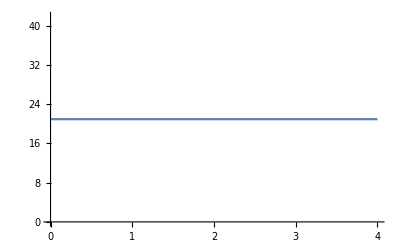

```mathematica
Plot[Coefficient[Subscript[M, t]/Subscript[χ, z]/.sol,a^3  G s]/.{a->1},{x,0,4}]
```

## # Bredt Singola cella

```mathematica
trattiAperti={{lunghezza, spessore}, {(√3)/2 a, s}, {(√3)/2 a, s}, {a, s}, {a, s}}[[2;;]];
trattiChiusi={{lunghezza, spessore}, {0, 0}}[[2;;]];AreaRacchiusaDallaLineaMediaDellaCella=0;
momentoTorcenteDato={{Forza, Distanza CdT}, {F, 0.31a}}[[2;;]];
```

### Calcoli

```mathematica
momentoTorcenteDatoCalcolato=momentoTorcenteDato[[1,1]]*momentoTorcenteDato[[1,2]]
ItorsioneAperti=∑_(i=1)^Length[trattiAperti] (trattiAperti[[i,1]]*trattiAperti[[i,2]]^3)/3
circolazioneChiusi=∑_(i=1)^Length[trattiChiusi] trattiChiusi[[i,1]];
ItorsioneChiusi=4s*AreaRacchiusaDallaLineaMediaDellaCella^2/circolazioneChiusi

momentoTorcenteAperti=Subscript[Gχ, t] ItorsioneAperti;
momentoTorcenteChiuso=If[Length[trattiChiusi]==1,0,Subscript[Gχ, t]*ItorsioneChiusi]

problemaTorcente=momentoTorcenteDatoCalcolato==momentoTorcenteAperti+momentoTorcenteChiuso
soluzioneTorcente=Solve[problemaTorcente,Subscript[Gχ, t]]//Flatten
τaperto=momentoTorcenteDatoCalcolato/ItorsioneAperti*s
τchiuso=momentoTorcenteChiuso/(2*AreaRacchiusaDallaLineaMediaDellaCella*s)


displayBredt=TableForm[{{momentoTorcenteAperti, "BOH"}, {momentoTorcenteChiuso, "BOH"}, {problemaTorcente, "BOH"}, {soluzioneTorcente, "BOH"}, {τaperto, τaperto//N}, {τchiuso, "BOH"}},TableHeadings->{{{"Momento torcente dei tratti aperti"}, {"Momento torcente dei tratti chiusi"}, {"Equazione del momento torcente"}, {"Soluzione"}, {"τ Aperto"}, {"τ Chiuso"}},{None,None}}];
```

0.31 a F

(2 a s^3)/3+(a s^3)/(√3)

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

0

0.31 a F==((2 a s^3)/3+(a s^3)/(√3)) Gχ_t

{Gχ_t→(0.249193 F)/s^3}

(0.31 a F s)/((2 a s^3)/3+(a s^3)/(√3))

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

### Display

```mathematica
displayBredt
```

| None | None
{Momento torcente dei tratti aperti} | ((2 a s^3)/3+(a s^3)/(√3)) Gχ_t | BOH
{Momento torcente dei tratti chiusi} | 0 | BOH
{Equazione del momento torcente} | 0.31 a F==((2 a s^3)/3+(a s^3)/(√3)) Gχ_t | BOH
{Soluzione} | Gχ_t→(0.249193 F)/s^3 | BOH
{τ Aperto} | (0.31 a F s)/((2 a s^3)/3+(a s^3)/(√3)) | (0.249193 F)/s^2
{τ Chiuso} | Indeterminate | BOH